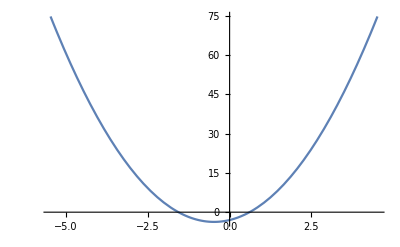
-Graphics--3/(2 π)

```mathematica
With[{func=Pi x^2+3x-3},
With[{topX=Solve[D[func,x]==0,x][[1,1,2]]},
Labeled[Plot[func,{x,topX-5,topX+5}, GridLines->{Append[Table[t,{t,topX-5,topX+5}],{topX,Directive[Red,Thick]}],Automatic}],Style[TraditionalForm[topX],Bold,20]]]
]
```

```mathematica
Solve[D[x-x^2,x]==0,x]
```

{{x→1/2}}

```mathematica
BernsteinBasis[4,2,x]//PiecewiseExpand
```

Piecewise[{{6 (-1+x)^2 x^2, 0<x<1}, {0, True}}]

```mathematica
Table[BernsteinBasis[d,n,x]//PiecewiseExpand,{d,10},{n,d}]
```

{{Piecewise[{{1, x==1}, {x, 0<x<1}, {0, True}}]},{Piecewise[{{-2 (-1+x) x, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^2, 0<x<1}, {0, True}}]},{Piecewise[{{3 (-1+x)^2 x, 0<x<1}, {0, True}}],Piecewise[{{-3 (-1+x) x^2, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^3, 0<x<1}, {0, True}}]},{Piecewise[{{-4 (-1+x)^3 x, 0<x<1}, {0, True}}],Piecewise[{{6 (-1+x)^2 x^2, 0<x<1}, {0, True}}],Piecewise[{{-4 (-1+x) x^3, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^4, 0<x<1}, {0, True}}]},{Piecewise[{{5 (-1+x)^4 x, 0<x<1}, {0, True}}],Piecewise[{{-10 (-1+x)^3 x^2, 0<x<1}, {0, True}}],Piecewise[{{10 (-1+x)^2 x^3, 0<x<1}, {0, True}}],Piecewise[{{-5 (-1+x) x^4, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^5, 0<x<1}, {0, True}}]},{Piecewise[{{-6 (-1+x)^5 x, 0<x<1}, {0, True}}],Piecewise[{{15 (-1+x)^4 x^2, 0<x<1}, {0, True}}],Piecewise[{{-20 (-1+x)^3 x^3, 0<x<1}, {0, True}}],Piecewise[{{15 (-1+x)^2 x^4, 0<x<1}, {0, True}}],Piecewise[{{-6 (-1+x) x^5, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^6, 0<x<1}, {0, True}}]},{Piecewise[{{7 (-1+x)^6 x, 0<x<1}, {0, True}}],Piecewise[{{-21 (-1+x)^5 x^2, 0<x<1}, {0, True}}],Piecewise[{{35 (-1+x)^4 x^3, 0<x<1}, {0, True}}],Piecewise[{{-35 (-1+x)^3 x^4, 0<x<1}, {0, True}}],Piecewise[{{21 (-1+x)^2 x^5, 0<x<1}, {0, True}}],Piecewise[{{-7 (-1+x) x^6, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^7, 0<x<1}, {0, True}}]},{Piecewise[{{-8 (-1+x)^7 x, 0<x<1}, {0, True}}],Piecewise[{{28 (-1+x)^6 x^2, 0<x<1}, {0, True}}],Piecewise[{{-56 (-1+x)^5 x^3, 0<x<1}, {0, True}}],Piecewise[{{70 (-1+x)^4 x^4, 0<x<1}, {0, True}}],Piecewise[{{-56 (-1+x)^3 x^5, 0<x<1}, {0, True}}],Piecewise[{{28 (-1+x)^2 x^6, 0<x<1}, {0, True}}],Piecewise[{{-8 (-1+x) x^7, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^8, 0<x<1}, {0, True}}]},{Piecewise[{{9 (-1+x)^8 x, 0<x<1}, {0, True}}],Piecewise[{{-36 (-1+x)^7 x^2, 0<x<1}, {0, True}}],Piecewise[{{84 (-1+x)^6 x^3, 0<x<1}, {0, True}}],Piecewise[{{-126 (-1+x)^5 x^4, 0<x<1}, {0, True}}],Piecewise[{{126 (-1+x)^4 x^5, 0<x<1}, {0, True}}],Piecewise[{{-84 (-1+x)^3 x^6, 0<x<1}, {0, True}}],Piecewise[{{36 (-1+x)^2 x^7, 0<x<1}, {0, True}}],Piecewise[{{-9 (-1+x) x^8, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^9, 0<x<1}, {0, True}}]},{Piecewise[{{-10 (-1+x)^9 x, 0<x<1}, {0, True}}],Piecewise[{{45 (-1+x)^8 x^2, 0<x<1}, {0, True}}],Piecewise[{{-120 (-1+x)^7 x^3, 0<x<1}, {0, True}}],Piecewise[{{210 (-1+x)^6 x^4, 0<x<1}, {0, True}}],Piecewise[{{-252 (-1+x)^5 x^5, 0<x<1}, {0, True}}],Piecewise[{{210 (-1+x)^4 x^6, 0<x<1}, {0, True}}],Piecewise[{{-120 (-1+x)^3 x^7, 0<x<1}, {0, True}}],Piecewise[{{45 (-1+x)^2 x^8, 0<x<1}, {0, True}}],Piecewise[{{-10 (-1+x) x^9, 0<x<1}, {0, True}}],Piecewise[{{1, x==1}, {x^10, 0<x<1}, {0, True}}]}}